```mathematica
Clear["Global`*"]
```

### 関数

```mathematica
LoopMatrix[g_]:=(
FundLoop=FindFundamentalCycles[UndirectedGraph[g]];
RuleFundLoop=Table[EdgeRules[FundLoop[[i]]],{i,Length[FundLoop]}];
RuleRevFundLoop=Table[
EdgeRules[ReverseGraph[Graph[RuleFundLoop[[i]]]]],
{i,Length[FundLoop]}
];
Ruleg=EdgeRules[g];
Table[
Table[
If[MemberQ[RuleFundLoop[[j]],Ruleg[[i]]],1,0]+If[MemberQ[RuleRevFundLoop[[j]],Ruleg[[i]]],-1,0],
{i,EdgeCount[g]}
],
{j,Length[FundLoop]}]
)
```

```mathematica
VertexSortFromLoopEdgeList[LoopEdgeList_]:=(
UndirectedLoop=FindCycle[UndirectedGraph[LoopEdgeList]][[1]];
MinVertexNum=Min[VertexList[UndirectedLoop]];
VertexLoop={MinVertexNum};
For[j=1,Length[VertexLoop]≠ Length[UndirectedLoop],j++,
VertexLoop=Append[VertexLoop,UndirectedLoop[[FirstPosition[UndirectedLoop,VertexLoop[[j]]<->_][[1]],2]]]
];
VertexLoop=Append[VertexLoop,MinVertexNum]
)(* Vertex Sort From Loop Edge List ルールエッジで表現された巡回路から、頂点で表現された巡回路に直す *)
```

```mathematica
PartLoopByGreedyFromSort[SortList_]:=((* 入力として枝のコストの順位を与えられたときのGreedyを使った部分巡回路の構築 *)
EdgeSolution={};
EdgeProcess={Ruleg[[SortList[[1]]]]};
For[j=2,
EdgeSolution=={},
j++,
AppendEdgeProcess=Append[EdgeProcess,Ruleg[[SortList[[j]]]]];
If[Max[VertexDegree[AppendEdgeProcess]]≤2,
If[AcyclicGraphQ[UndirectedGraph[AppendEdgeProcess]],
EdgeProcess=AppendEdgeProcess,
EdgeSolution=AppendEdgeProcess
]
]
];
EdgeSolution=EdgeRules[FindCycle[UndirectedGraph[EdgeSolution]][[1]]];
VertexSortFromLoopEdgeList[EdgeSolution]
)
```

```mathematica
DelEle[list_,element_]:=list/.element->Nothing(* Delete Element *)
```

```mathematica
DelEleList[list_,elementlist_]:=list/.Table[i-> Nothing ,{i,elementlist}](* Delete Element *)
```

```mathematica
DelEdgeVertexList[edgelist_,vertexlist_]:=(
devl={};(* Variable of DelEdgeVertexList *)
Do[devl=Union[Position[edgelist,i].{{1},{0}},devl],{i,vertexlist}];
Delete[edgelist,devl]
)(* Delete Edge list from Vertex List 頂点リストから枝リストを削除（頂点リストにある頂点で構成される枝はすべて枝リストから削除）頂点リストに重複があってもUnionがあるのでOK *)
```

```mathematica
EdgeNum[Edge_]:=(
FirstPosition[EdgeRules[Gin],Edge,
FirstPosition[
EdgeRules[Gin],
EdgeRules[
ReverseGraph[{Edge}]
][[1]]
]
][[1]]
) (* Edge Number *)
```

```mathematica
EdgeNumList[Edge_]:=Table[EdgeNum[Edge[[i]]],{i,Length[Edge]}] (* Edge Number List *)
```

```mathematica
EdgeD[Edge_]:=PD[[EdgeNum[Edge]]](* Edge Distance *)
```

```mathematica
EdgeDList[Edge_]:=PD[[EdgeNumList[Edge]]](* Edge Distance *)
```

```mathematica
ListPosRef[list1_,list2_,element_]:=list1[[FirstPosition[list2,element][[1]]]](* list2でのelementの位置に来る、list1の要素を求める(list1にlist2の位置を反映 List Position Reflection) *)
```

```mathematica
EdgeReconst[Edge1_,Side1_,Edge2_,Side2_]:=VertexList[{Edge1}][[Side1]]->VertexList[{Edge2}][[Side2]](* Edge Reconstraction ２つの枝のそれぞれ片方の頂点を使って枝を再構成する *)
```

```mathematica
RestVertex[PartLoop_]:=Delete[VertexList[Gin],Table[{VertexList[PartLoop][[i]]},{i,Length[VertexList[PartLoop]]}]]
```

```mathematica
TriTourDiff[Edge_,Vertex_]:=(
EdgeD[VertexList[{Edge}][[1]]->Vertex]+EdgeD[VertexList[{Edge}][[2]]->Vertex]-EdgeD[Edge]
)(* Triangle Tour Difference *)
```

```mathematica
TriTourDiffList[PartLoop_,Vertex_]:=Table[TriTourDiff[PartLoop[[i]],Vertex],{i,Length[PartLoop]}]
```

```mathematica
MinTriTourDiffPosition[PartLoop_,Vertex_]:=(
FirstPosition[TriTourDiffList[PartLoop,Vertex],Min[TriTourDiffList[PartLoop,Vertex]]][[1]]
)
```

```mathematica
MinEdgeReconstPair[EdgePair_]:=(
ReconstEdgeD1=EdgeD[EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],1]]+EdgeD[EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],2]];
ReconstEdgeD2=EdgeD[EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],2]]+EdgeD[EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],1]];
If[
ReconstEdgeD1<ReconstEdgeD2,
{ReconstEdgeD1,{EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],1],EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],2]}},
{ReconstEdgeD2,{EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],2],EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],1]}}
]
)(* Minimum Edge Reconstraction Pair 枝ペアを再構成し、枝のコストが小さいほうのコストと枝ペアを出力 *)
```

```mathematica
SquareTourDiff[Edge1_,Edge2_]:=(
MinEdgeReconstPair[{Edge1,Edge2}][[1]]-EdgeD[Edge1]-EdgeD[Edge2]
)(* Square Tour Difference *)
```

```mathematica
SquareTourDiffList[PartLoop1_,PartLoop2_]:=Table[SquareTourDiff[i,j],{i,PartLoop1},{j,PartLoop2}]
```

```mathematica
MinSquareTourDiffEdgePair[PartLoop1_,PartLoop2_]:=(
PairNum=FirstPosition[SquareTourDiffList[PartLoop1,PartLoop2],Min[SquareTourDiffList[PartLoop1,PartLoop2]]];
{PartLoop1[[PairNum[[1]]]],PartLoop2[[PairNum[[2]]]]}
)(* 最小のスクエアツアとなるPartLoopの枝ペア *)
```

```mathematica
JoinPartLoop[PartLoop1_,PartLoop2_]:=Join[DelEleList[Join[PartLoop1,PartLoop2],MinSquareTourDiffEdgePair[PartLoop1,PartLoop2]],MinEdgeReconstPair[MinSquareTourDiffEdgePair[PartLoop1,PartLoop2]][[2]]]
```

```mathematica
PartLoopByNewUndirectedGreedyFromSort[SortList_]:=((* 枝の向きを考慮しない、入力として枝のコストの順位を与えられたときの新しいGreedyを使った部分巡回路の構築(コストは優先順位が高い順にソートされる:ランク) *)
EdgeSolution={};
For[i=3,Length[EdgeSolution]==0,i++,
EdgeSolution=FindCycle[
UndirectedGraph[EdgeList[Gout][[SortList[[Range[i]]]]]],
Infinity,All];
];
EdgeSolution=EdgeRules[EdgeSolution[[1]]];
VertexSortFromLoopEdgeList[EdgeSolution]
)
```

```mathematica
PartLoopByNewDirectedGreedyFromSort[SortList_]:=((* 枝の向きを考慮する、入力として枝のコストの順位を与えられたときの新しいGreedyを使った部分巡回路の構築(コストは優先順位が高い順にでソートされる) *)
EdgeSolution={};
For[i=3,Length[EdgeSolution]==0,i++,
EdgeSolution=FindCycle[
Graph[EdgeList[Gout][[SortList[[Range[i]]]]]],
Infinity,All];
];
EdgeSolution=EdgeRules[EdgeSolution[[1]]];
VertexSortFromLoopEdgeList[EdgeSolution]
)
```

```mathematica
RestEdgeSort[Edge_,Cost_]:=
EdgeNumList[DelEdgeVertexList[Ruleg,VertexList[Edge]]][[
Ordering[Cost[[
EdgeNumList[DelEdgeVertexList[Ruleg,VertexList[Edge]]
]]]]
]](* 残りの枝でのソート(与えられた枝をRulegから引いたエッジリストの中でのソート) *)
```

```mathematica
RestVertexMinCost[PartLoop_]:=Table[Min[TriTourDiffList[PartLoop,i]],{i,RestVertex[PartLoop]}](* 残りの頂点のそれぞれの追加コストが最小になる位置での追加コストのリスト *)
```

```mathematica
MinRestVertex[PartLoop_]:=RestVertex[PartLoop][[
FirstPosition[RestVertexMinCost[PartLoop],Min[RestVertexMinCost[PartLoop]]][[1]]
]](* 残りの頂点の中でも最小の追加コストとなる頂点 *)
```

```mathematica
LoopDelEdge[PartLoop_]:=PartLoop[[MinTriTourDiffPosition[PartLoop,MinRestVertex[PartLoop]]]](* 頂点を追加するときに削除すべき枝 *)
```

```mathematica
InsertVertexLoop[PartLoop_]:=EdgeRules[EdgeAdd[EdgeDelete[PartLoop,LoopDelEdge[PartLoop]],{VertexList[{LoopDelEdge[PartLoop]}][[1]]-> MinRestVertex[PartLoop],MinRestVertex[PartLoop]-> VertexList[{LoopDelEdge[PartLoop]}][[2]]}]](* １つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
ContinuousInsertVertexLoop[PartLoop_]:=(
PartLoopSolution={PartLoop};
For[j=1,Min[RestVertexMinCost[PartLoopSolution[[-1]]]]≤1,
PartLoopSolution=Append[PartLoopSolution,InsertVertexLoop[PartLoopSolution[[-1]]]]
];
PartLoopSolution)(* 連続で１つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
OutVertex[PartLoop_]:=Table[If[!RegionMember[
Polygon[Pin[[VertexSortFromLoopEdgeList[PartLoop]]]],Pin[[i]]
],i],{i,Range[Length[Pin]]}]/.Null->Nothing(* PartLoopの外側の頂点 *)
```

```mathematica
OutEdgeSortEdgeList[PartLoop_,Cost_]:=(
EdgeExceptInner=DelEdgeVertexList[Ruleg,
DelEleList[
Table[If[RegionMember[
Polygon[Pin[[VertexSortFromLoopEdgeList[PartLoop]]]],Pin[[i]]
],i],{i,Range[Length[Pin]]}]/.Null->Nothing,
VertexList[PartLoop]]
];(* PartLoopの内側の頂点を除いた頂点で構成される枝リストの変数 *)
OutEdge={};(* OutEdge is Variable *)
Do[OutEdge=Union[EdgeExceptInner[[Flatten[Position[EdgeExceptInner,i].{{1},{0}}]]],OutEdge],{i,OutVertex[PartLoop]}];
EdgeRules[Gout][[EdgeNumList[OutEdge][[Ordering[Cost[[EdgeNumList[OutEdge]]]]]]]]
)(* 部分巡回路よりも外側の頂点を見つけ、それらの頂点を含む枝のコストソートをルールエッジリストで出力 *)
```

```mathematica
InsertDetachedEdge[PartLoop_,DetachedEdge_]:=Join[DelEleList[Append[PartLoop,DetachedEdge],{MinSquareTourDiffEdgePair[PartLoop,{DetachedEdge}][[1]]}],MinEdgeReconstPair[MinSquareTourDiffEdgePair[PartLoop,{DetachedEdge}]][[2]]](* PartLoopのどの頂点にも接していない枝を挿入 *)
```

```mathematica
EdgeLoopSide[PartLoop_,ContactEdge_]:=Intersection[VertexList[PartLoop],VertexList[{ContactEdge}]][[1]](* PartLoopに接する枝のPartLoop側の頂点 *)
```

```mathematica
EdgeRestSide[PartLoop_,ContactEdge_]:=DelEle[VertexList[{ContactEdge}],EdgeLoopSide[PartLoop,ContactEdge]][[1]](* PartLoopに接する枝のPartLoop側でない頂点 *)
```

```mathematica
DelEdgeContactEdge[PartLoop_,ContactEdge_]:=PartLoop[[MinTriTourDiffPosition[PartLoop,EdgeRestSide[PartLoop,ContactEdge]]]](* PartLoopに接する枝を挿入する際に削除すべき枝 *)
```

```mathematica
InsertContactEdge[PartLoop_,ContactEdge_]:=Join[DelEle[PartLoop,DelEdgeContactEdge[PartLoop,ContactEdge]],{ContactEdge,EdgeRestSide[PartLoop,ContactEdge]->DelEle[VertexList[{DelEdgeContactEdge[PartLoop,ContactEdge]}],EdgeLoopSide[PartLoop,ContactEdge]][[1]]}](* PartLoopの頂点に接する枝を挿入 *)
```

```mathematica
InsertEdge[PartLoop_,ContactEdge_]:=If[IntersectingQ[VertexList[PartLoop],VertexList[{ContactEdge}]],InsertContactEdge[PartLoop,ContactEdge],InsertDetachedEdge[PartLoop,ContactEdge]](* PartLoopの頂点に接する枝か否かを判定し、枝を挿入 *)
```

```mathematica
EdgeNumListVertex[VertexPairList_]:=EdgeNumList[Table[i[[1]]-> i[[2]],{i,VertexPairList}]](* Edge Num List from Vertex 枝の頂点ペアのリストから枝番号のリストを出力 *)
```

```mathematica
NewDirectedGreedyFromSort[SortList_]:=((* 入力として枝のコストの順位を与えられたときのGreedyを使ったすべての頂点を含む巡回路の構築 *)
EdgeProcess={};
PartLoopVertexProcess={};(* 過程におけるすべての有効グラフの閉路の頂点リスト *)
For[j=1,
Length[PartLoopVertexProcess]≠ Length[Pin],
j++,
If[!SubsetQ[PartLoopVertexProcess,VertexList[{EdgeRules[Gout][[SortList[[j]]]]}]],
EdgeProcess=Append[EdgeProcess,EdgeRules[Gout][[SortList[[j]]]]]
];
PartLoopVertexProcess=VertexList[Flatten[PartLoopProcess=FindCycle[Graph[EdgeProcess],Infinity,All]]];
];
PartLoopProcess
)
```

```mathematica
DelEdgeNumOfRestPartLoop[EdgeListNum_,PartLoop_]:=DelEleList[EdgeListNum,DelEleList[EdgeNumListVertex[Subsets[VertexList[PartLoop],{2}]],EdgeNumList[PartLoop]]](* PartLoopを構成する枝ではないがPartLoopの頂点で構成されるすべての枝を枝リストの枝番号から削除する *)
```

```mathematica
NewDirectedGreedyFromSort2[SortList_]:=((* 入力として枝のコストの順位を与えられたときのGreedyを使ったすべての頂点を含む巡回路の構築2(枝を追加してから余分な枝を削除するアルゴリズム) *)
EdgeProcessNum={};
PartLoopVertexProcess={};(* 過程におけるすべての有効グラフの閉路の頂点リスト *)
DelEdgeProcess={};
For[j=1,Length[PartLoopVertexProcess]< Length[Pin],j++,
EdgeProcessNum=Append[EdgeProcessNum,SortList[[j]]];
PartLoopVertexProcess=VertexList[Flatten[PartLoopProcess=FindCycle[Graph[EdgeRules[Gout][[EdgeProcessNum]]],Infinity,All]]];
DelEdge={};
For[k=1,k≤Length[PartLoopProcess],k++,
tmp=EdgeProcessNum;
EdgeProcessNum=DelEdgeNumOfRestPartLoop[tmp,EdgeRules[PartLoopProcess[[k]]]];
DelEdge=Join[DelEdge,DelEleList[tmp,EdgeProcessNum]]
];
DelEdgeProcess=Append[DelEdgeProcess,DelEdge];
PartLoopVertexProcess=VertexList[Flatten[PartLoopProcess=FindCycle[Graph[EdgeRules[Gout][[EdgeProcessNum]]],Infinity,All]]]
];
PartLoopProcess
)
```

```mathematica
ComplementIntersection[List1_,List2_]:=Complement[List1∪List2,List1∩List2](* 2つのリストの共通集合の補集合を求める *)
```

```mathematica
EdgeRulesList[GraphList_]:=Table[EdgeRules[GraphList[[i]]],{i,Length[GraphList]}](* <->や->で表現されるグラフリストを枝の規則のリスト群に変換する *)
```

```mathematica
PluralPartLoopByGreedyFromRank[Rank_]:=(
PartLoopProcess={};
For[i=3,Length[PartLoopProcess]==0,i++,
PartLoopProcess=FindCycle[
Graph[EdgeList[Gout][[Rank[[Range[i]]]]]],
Infinity,All]
];
EdgeRulesList[PartLoopProcess]
)
(* 入力として枝のランクを与えられたときのGreedyの応用による複数の部分巡回路の構築 *)
```

```mathematica
DelEdgePluralPartLoop[PartLoopList_]:=(
EdgeProcessNum=EdgeNumList[Flatten[PartLoopList]];
DelEdge={};
For[k=1,k≤Length[PartLoopList],k++,
tmp=EdgeProcessNum;
EdgeProcessNum=DelEdgeNumOfRestPartLoop[tmp,PartLoopList[[k]]];
DelEdge=Join[DelEdge,DelEleList[tmp,EdgeProcessNum]]
];
EdgeRulesList[FindCycle[Graph[EdgeRules[Gout][[EdgeProcessNum]]],Infinity,All]]
)
(* Delete Edge from Plural PartLoop, 複数の部分巡回路から、PartLoopを構成する枝ではないがPartLoopの頂点で構成されるすべての枝を削除し、再度、複数の部分巡回路を見つける *)
```

```mathematica
PluralPartLoopByGreedyFromRank2[Rank_]:=(
DelEdge={};
EdgeProcess={};
PartLoopProcess={};
For[i=1,PartLoopProcess=={},i++,
AddEdge=EdgeRules[Gout][[Rank[[i]]]];
If[(PartLoopProcess=FindCycle[Graph[Append[EdgeProcess,AddEdge]],Infinity,All])=={},
If[FindCycle[UndirectedGraph[Append[EdgeProcess,AddEdge]],Infinity,All]=={},
EdgeProcess=Append[EdgeProcess,AddEdge],
DelEdge=Append[DelEdge,AddEdge];
]
]
];
EdgeRulesList[PartLoopProcess][[1]]
)
(* 入力として枝のランクを与えられたときのGreedyの応用による複数の部分巡回路の構築2(有向閉路ではないが無向閉路となるとき枝を加えない) *)
```

### 渦電流の計算

```mathematica
Pin={{3.30204,9.09128},{3.30442,0.46863},{9.01646,6.24185},{9.31342,1.24199},{6.10577,2.96787},{5.75196,4.97666},{3.32525,5.95897},{1.84868,1.18248},{7.3017,7.41784},{4.80162,2.52861}}
(*Point input*)
```

{{3.30204,9.09128},{3.30442,0.46863},{9.01646,6.24185},{9.31342,1.24199},{6.10577,2.96787},{5.75196,4.97666},{3.32525,5.95897},{1.84868,1.18248},{7.3017,7.41784},{4.80162,2.52861}}

```mathematica
Gin=DirectedGraph[CompleteGraph[Length[Pin],VertexLabels->"Name",EdgeLabels->"Name"],"Acyclic"];
```

```mathematica
h=LoopMatrix[Gin];
PD=Table[
EuclideanDistance[
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[1,1]]]],
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[2,1]]]]
],
{i,Length[EdgeRules[Gin]]}];(* Point Distance *)
r=IdentityMatrix[Length[EdgeRules[Gin]]]PD;
s=Table[0,{i,Length[EdgeRules[Gin]]}];
FLP=Table[
Pin[[
ConnectedComponents[RuleFundLoop[[i]]][[1]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Point *)
LoopSpin=Table[
If[(Append[FLP[[i,2]]-FLP[[i,1]],0]×Append[FLP[[i,3]]-FLP[[i,2]],0]).{0,0,1}>0,1,-1],
{i,Length[RuleFundLoop]}];(* 右回りならば負、左回りならば正 *)
FLA=Table[
Area[Polygon[
Pin[[ConnectedComponents[RuleFundLoop[[i]]][[1]]]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Area *)
U=Table[LoopSpin[[i]]FLA[[i]],{i,Length[RuleFundLoop]}];(* 誘導起電力は右回りなら負、左回りなら正 *)
Curr=Transpose[h].Inverse[h.r.Transpose[h]].(h.s+U);(* 誘導起電力行列を考慮した電流を求める式 *)
```

```mathematica
Gout=Graph[Table[If[Curr[[i]]>0,
VertexList[{EdgeRules[Gin][[i]]}][[1]]->VertexList[{EdgeRules[Gin][[i]]}][[2]],
VertexList[{EdgeRules[Gin][[i]]}][[2]]->VertexList[{EdgeRules[Gin][[i]]}][[1]]
],{i,Length[EdgeRules[Gin]]}
]];(* 電流値の正負をグラフの向きに反映した出力グラフ *)
```

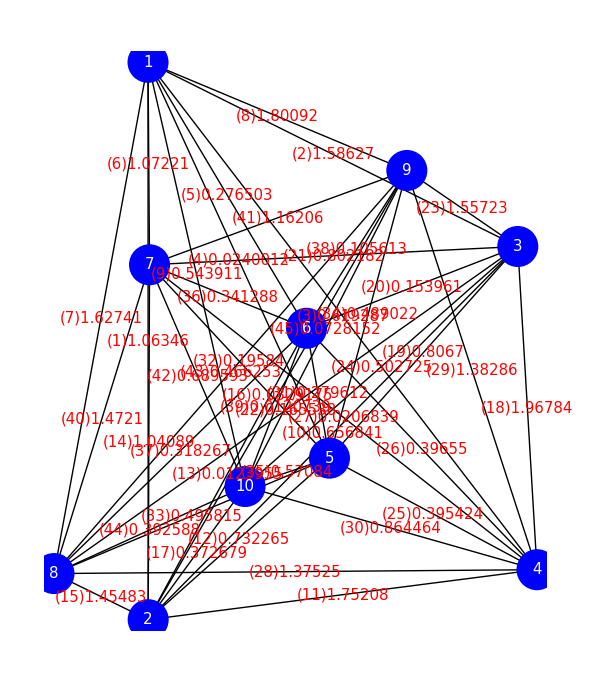

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gout][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gout][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gout]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[Style["("<>TextString[i]<>")"<>TextString[Abs[Curr[[i]]]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```

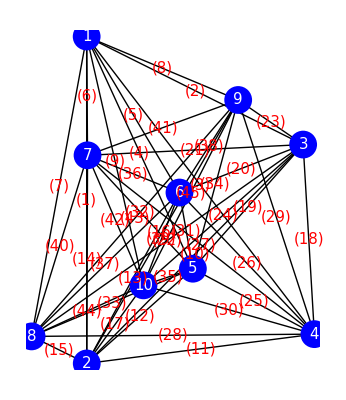

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gout][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gout][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gout]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[Style["("<>TextString[i]<>")",FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```

### TSPの解

```mathematica
Grid[{EdgeRules[Gin][[1;;10]],Range[10]},Frame->All]
Grid[{EdgeRules[Gin][[11;;20]],Range[11,20]},Frame->All]
Grid[{EdgeRules[Gin][[21;;30]],Range[21,30]},Frame->All]
Grid[{EdgeRules[Gin][[31;;40]],Range[31,40]},Frame->All]
Grid[{EdgeRules[Gin][[41;;45]],Range[41,45]},Frame->All]
```

1→2 | 1→3 | 1→4 | 1→5 | 1→6 | 1→7 | 1→8 | 1→9 | 1→10 | 2→3
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10

2→4 | 2→5 | 2→6 | 2→7 | 2→8 | 2→9 | 2→10 | 3→4 | 3→5 | 3→6
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20

3→7 | 3→8 | 3→9 | 3→10 | 4→5 | 4→6 | 4→7 | 4→8 | 4→9 | 4→10
21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30

5→6 | 5→7 | 5→8 | 5→9 | 5→10 | 6→7 | 6→8 | 6→9 | 6→10 | 7→8
31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40

7→9 | 7→10 | 8→9 | 8→10 | 9→10
41 | 42 | 43 | 44 | 45

```mathematica
Curr
```

{1.06346,-1.58627,-0.619287,-0.0240012,-0.276503,1.07221,1.62741,-1.80092,0.543911,0.656841,1.75208,0.732265,0.0123955,-1.04089,-1.45483,0.0329175,0.372679,-1.96784,-0.8067,0.153961,0.802182,-0.165538,1.55723,-0.502725,-0.395424,0.39655,0.0206839,-1.37525,1.38286,-0.864464,0.279612,-0.19584,-0.495815,0.489022,-0.57084,0.341288,0.318267,-0.105613,0.0120739,1.4721,-1.16206,0.689593,-0.466253,0.392588,-0.0728152}

```mathematica
Reverse[Ordering[Abs[Curr]]](* 降順 *)
```

{18,8,11,7,2,23,40,15,29,28,41,6,1,14,30,19,21,12,42,10,3,35,9,24,33,34,43,26,25,44,17,36,37,31,5,32,22,20,38,45,16,4,27,13,39}

```mathematica
PDSort=Ordering[PD//N](* 昇順 *)
```

{35,15,31,23,17,36,39,38,6,44,20,25,42,12,32,41,8,19,34,33,30,5,40,18,13,26,37,14,45,24,21,11,2,29,9,4,28,27,16,7,10,43,1,22,3}

```mathematica
PDCurrCost=Abs[PD/Curr ]
```

{8.10813,4.02544,15.9647,280.601,17.319,2.92144,4.94113,2.40745,12.3767,12.3644,3.45792,5.12678,413.827,5.27469,1.11445,243.544,6.83321,2.54526,5.43047,22.7401,7.10342,53.,1.33523,11.1735,9.21159,13.0137,368.541,5.42808,4.69696,5.42725,7.29478,20.8531,9.31058,9.42262,2.41073,7.6709,17.1035,27.3788,217.498,3.39617,3.64491,5.41562,17.766,8.26641,75.4149}

```mathematica
PDCurrCostSort=Ordering[PDCurrCost](* 昇順 *)
```

{15,23,8,35,18,6,40,11,41,2,29,7,12,14,42,30,28,19,17,21,31,36,1,44,25,33,34,24,10,9,26,3,37,5,43,32,20,38,22,45,39,16,4,27,13}

```mathematica
FindShortestTour[Pin]
Graphics[Line[Pin[[Last[%]]]]]
```

{31.515,{1,9,3,4,2,8,10,5,6,7,1}}

-Graphics-

### 一貫した新しいgreedyを用いた解法

```mathematica
CurrSort=Ordering[Abs[1/Curr]//N]
```

{18,8,11,7,2,23,40,15,29,28,41,6,1,14,30,19,21,12,42,10,3,35,9,24,33,34,43,26,25,44,17,36,37,31,5,32,22,20,38,45,16,4,27,13,39}

```mathematica
NewDirectedGreedyFromSort[PDCurrCostSort]
```

{{10->5,5->6,6->7,7->10},{8->2,2->5,5->6,6->7,7->8},{3->9,9->1,1->7,7->10,10->4,4->3},{3->9,9->1,1->7,7->10,10->5,5->3},{8->2,2->4,4->3,3->9,9->1,1->7,7->8},{8->2,2->5,5->3,3->9,9->1,1->7,7->8}}

```mathematica
LoopNum=j
```

23

```mathematica
DelEdgeNumOfRestPartLoop[PDCurrCostSort[[;;LoopNum-1]],EdgeRules[{8->2,2->5,5->3,3->9,9->1,1->7,7->8}]]
```

{15,23,8,35,18,6,40,11,29,12,42,30,28,19,17,31,36}

```mathematica
DelEdgeNumOfRestPartLoop[{15,23,8,35,18,6,40,11,29,12,42,30,28,19,17,31},EdgeRules[{8->2,2->4,4->3,3->9,9->1,1->7,7->8}]]
```

{15,23,8,35,18,6,40,11,12,42,30,19,17,31}

```mathematica
EdgeRules[Gout][[{15,23,8,35,18,6,40,11,12,42,30,19,17,31}]]
```

{8→2,3→9,9→1,10→5,4→3,1→7,7→8,2→4,2→5,7→10,10→4,5→3,2→10,5→6}

```mathematica
FindCycle[Graph[EdgeRules[Gout][[{15,23,8,35,18,6,40,11,12,42,30,19,17,31}]]],Infinity,All]
```

{{3->9,9->1,1->7,7->10,10->4,4->3},{3->9,9->1,1->7,7->10,10->5,5->3},{8->2,2->4,4->3,3->9,9->1,1->7,7->8},{8->2,2->5,5->3,3->9,9->1,1->7,7->8},{8->2,2->10,10->4,4->3,3->9,9->1,1->7,7->8},{8->2,2->10,10->5,5->3,3->9,9->1,1->7,7->8}}

```mathematica
Table[VertexList[i],{i,NewDirectedGreedyFromSort[PDCurrCostSort]}]
```

{{10,5,6,7},{8,2,5,6,7},{3,9,1,7,10,4},{3,9,1,7,10,5},{8,2,4,3,9,1,7},{8,2,5,3,9,1,7}}

```mathematica
VertexSortFromLoopEdgeList[EdgeRules[{10->5,5->6,6->7,7->10}]]
Graphics[line=Line[Pin[[%]]]]
```

{5,10,7,6,5}

-Graphics-

```mathematica
VertexSortFromLoopEdgeList[EdgeRules[{8->2,2->5,5->6,6->7,7->8}]]
Graphics[line=Line[Pin[[%]]]]
```

{2,8,7,6,5,2}

-Graphics-

{1,9,3,4,10,7,1}

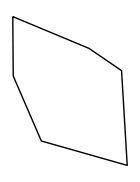

```mathematica
VertexSortFromLoopEdgeList[EdgeRules[{3->9,9->1,1->7,7->10,10->4,4->3}]]
Graphics[line=Line[Pin[[%]]]]
```

{1,9,3,5,10,7,1}

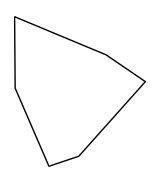

```mathematica
VertexSortFromLoopEdgeList[EdgeRules[{3->9,9->1,1->7,7->10,10->5,5->3}]]
Graphics[line=Line[Pin[[%]]]]
```

{1,9,3,4,2,8,7,1}

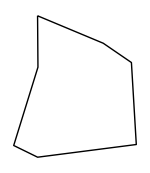

```mathematica
VertexSortFromLoopEdgeList[EdgeRules[{8->2,2->4,4->3,3->9,9->1,1->7,7->8}]]
Graphics[line=Line[Pin[[%]]]]
```

{1,9,3,5,2,8,7,1}

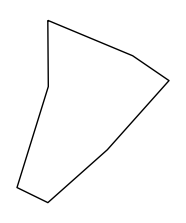

```mathematica
VertexSortFromLoopEdgeList[EdgeRules[{8->2,2->5,5->3,3->9,9->1,1->7,7->8}]]
Graphics[line=Line[Pin[[%]]]]
```

```mathematica
Show[-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-]
```

-Graphics-

### 一貫した新しいgreedyを用いた解法2

```mathematica
NewDirectedGreedyFromSort2[PDCurrCostSort]
```

{{8->2,2->10,10->5,5->6,6->7,7->8},{8->2,2->10,10->4,4->3,3->9,9->1,1->7,7->8},{8->2,2->10,10->5,5->3,3->9,9->1,1->7,7->8}}

```mathematica
DelEdgeProcess
```

{{},{},{},{},{},{},{},{},{41},{2},{29},{7},{},{14},{},{},{28},{},{11,42,12},{21},{},{}}

```mathematica
VertexSortFromLoopEdgeList[EdgeRules[{8->2,2->10,10->5,5->6,6->7,7->8}]]
Graphics[line=Line[Pin[[%]]]]
```

{2,8,7,6,5,10,2}

-Graphics-

```mathematica
VertexSortFromLoopEdgeList[EdgeRules[{8->2,2->10,10->4,4->3,3->9,9->1,1->7,7->8}]]
Graphics[line=Line[Pin[[%]]]]
```

{1,9,3,4,10,2,8,7,1}

-Graphics-

{1,9,3,5,10,2,8,7,1}

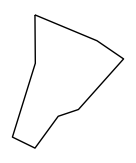

```mathematica
VertexSortFromLoopEdgeList[EdgeRules[{8->2,2->10,10->5,5->3,3->9,9->1,1->7,7->8}]]
Graphics[line=Line[Pin[[%]]]]
```

```mathematica
Show[-Graphics-,-Graphics-,-Graphics-]
```

-Graphics-

### 一貫した新しいgreedyを用いた解法3

{1,9,3,4,2,8,7,1}

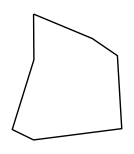

```mathematica
PartLoopByNewDirectedGreedyFromSort[PDCurrCostSort]
Graphics[line=Line[Pin[[%]]]]
```

```mathematica
DelEdgeVertexList[EdgeRules[Gout][[PDCurrCostSort]],{1,9,3,4,2,8,7,1}]
```

{10→5,5→6,6→10}

```mathematica
PartLoopByNewUndirectedGreedyFromSort[EdgeNumList[{10->5,5->6,6->10}]]
Graphics[line=Line[Pin[[%]]]]
```

{5,6,10,5}

-Graphics-

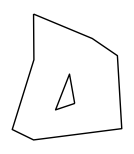

```mathematica
Show[-Graphics-,-Graphics-]
```

### 一貫した新しいgreedyを用いた解法4

```mathematica
PluralPartLoopByGreedyFromRank2[PDCurrCostSort]
```

{8→2,2→4,4→3,3→9,9→1,1→7,7→8}

{1,9,3,4,2,8,7,1}

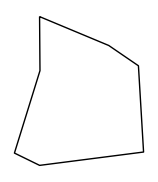

```mathematica
VertexSortFromLoopEdgeList[{8->2,2->4,4->3,3->9,9->1,1->7,7->8}]
Graphics[line=Line[Pin[[%]]]]
```